Université Pierre et Marie Curie |                                         | UE Transversale 1XM01Mathematica

__________________________________________________________________________

M 2 : Introduction à Mathematica
__________________________________________________________________________

## Exercices

## I. Calculs formels

### A. Fonctions essentielles

Dans les calculs ci-dessous, écrivez la suite des opérations que vous devez faire pour  pour aboutir au résultat, en faisant une étape (factorisation OU réduction au même dénominateur OU simplification OU réarrangement , etc ...)

#### 1. ==

→ Calculer au moyen d’une suite d’expressions :

```mathematica
1/(1/3+1/2)== 6/5
```

True

→ Calculer au moyen d’une suite d’expressions :

```mathematica
5/7-2/7(1-3/4) == 18/28
```

True

→ Expliquez dans les grandes lignes comment Mathematica parvient à ce type de résultat.

La function == indique si les expressions placées à droite et à gauche sont identiques.

→ Ces deux nombres sont très particuliers : en quoi ?
(si vous ne voyez pas, la suite des questions est dans la cellule cachée ci-dessous...)

```mathematica
N[(-7-4 √2-2 √(2 (10+7 √2)))]
N[(-7-4 √2+2 √(2 (10+7 √2)))]
```

-25.2741

-0.0395661

```mathematica
N[(-7-4 √2-2 √(2 (10+7 √2)))*(-7-4 √2+2 √(2 (10+7 √2)))]
```

1.

(-7-4 √2-2 √(2 (10+7 √2)))*(-7-4 √2+2 √(2 (10+7 √2)))

= (-7-4 √2) ^2 - 4(2(10+7 √2))
= 49 + 56 √2 + 32 - (80 +56 √2)
= 81 + 56 √2-80 -56 √2
= 1

```mathematica
N[(-7-4 √2-2 √(2 (10+7 √2)))*(-7-4 √2+2 √(2 (10+7 √2)))]==1
```

True

Montrer que le produit de ces 2 deux nombres vaut 1 :
	C’est facile à faire numériquement, mais vous n’avez pas prouvé que ce produit vaut exactement 1.
	Montrer que ce produit vaut exactement 1 au moyen d’une suite d’expressions.
Au total ces deux nombres sont exactement inverses l’un de l’autre, et s’écrivent avec les mêmes nombres.
La simplification que vous avez réalisée vous-même vous permet de comprendre (un peu) mieux comment ces deux nombres ont été construits. Ce que ne donne pas Mathematica a priori.

#### 3. Simplify

→ Expliquez ce que vous observez :

```mathematica
Sin[x]^2+Cos[x]^2
```

Cos[x]^2+Sin[x]^2

Mathematica ne peut pas calculer le formule

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

Le formule est simplifié par la function Simplify

```mathematica
Simplify[Sin[x]^2+Cos[x]^2==1]
```

True

Simplifiy peut faire aussi une simplification de justification

```mathematica
Simplify[Abs[Cos[x]]==Cos[x]]
```

Abs[Cos[x]]==Cos[x]

Le formule ne peut pas etre simplifé par mathématica

#### 4. Simplify avec Assumptions

→ Expliquez ce que vous observez :

Les assumptions ne sont pas assez fortes pour les simplifier

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], x>0]
Simplify[Abs[Cos[x]]==Cos[x], x<0]
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π]
```

Abs[Cos[x]]==Cos[x]

Abs[Cos[x]]==Cos[x]

Abs[Cos[x]]==Cos[x]

On peut aussi donner plusieurs suppositions avec les connecteurs logiques (&& veut dire ET, || veut dire OU) :

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π/2]
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2]
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2 && (-π/2+2π<x<π/2+2π)]
```

True

True

Simplify::cas: Warning: contradictory assumption(s) -π/2 < x < π/2 && 3\ π/2 < x < 5\ π/2 encountered.

True

→ En définitive quelle est la solution la plus simple (qui découle de la définition) ? Écrivez là :

Retenir :

```mathematica
Simplify[Sqrt[x^2]]
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],x≥0]
```

x

PowerExpand[] suppose toujours que x≥0 et donc :

```mathematica
PowerExpand[Sqrt[x^2]]
```

x

C’est donc une fonction très pratique si l’on est sûr que x est positif.

#### 5. Simplify avec Assumptions et Element

→ Expliquez :

```mathematica
Simplify[Sqrt[x^2],Element[x,Reals]]==Simplify[√(x^2),x∈Reals]==Abs[x]
Simplify[Element[x,Reals] == (x∈Reals)]
Simplify[Sqrt[x^2] == √(x^2)]
```

True

True

True

→ À quoi doit être égal ? ???  ci-dessous :

```mathematica
Simplify[Sin[x+2*n*Pi]==Sin[x] ,Element[n,Integers]]
```

True

```mathematica
Simplify[Cos[n*Pi/2-x]==Sin[x],Element[(n-1)/4,Integers]]
```

True

On peut aussi combiner Element[] avec d’autres conditions :

→ Quelles sont les hypothèses de travail de Mathematica ? :

→ Quelle est l’expression qui a un sens mathématique simple (avec les hypothèses de travail de Mathematica ) ? :

```mathematica
Simplify[Log[x^r]]
Simplify[Log[x^r],x>0]
Simplify[Log[x^r],Element[r,Reals]]
Simplify[Log[x^r],x>0&&Element[r,Reals]]
```

Log[x^r]

Log[x^r]

Log[x^r]

r Log[x]

→ Comment se simplifie l’expression suivante : 5 ln a^2− 2 ln a ?

```mathematica
Simplify[5Log[a^2]-2Log[a],a>0]
```

8 Log[a]

### B. Fonction pure

#### 1. Définition

→ Qu’est-ce qu’une fonction pure dans Mathematica ? :

Les fonctions anonymes, encore appelées fonctions pures dans Mathematica, sont des fonctions qui n’ont pas de nom. 
En pratique c’est le code même de la fonction qui est utilisé comme moyen d’utiliser la fonction.

→ Construire une fonction pure qui ne retient que les nombres multiples de 4 augmentés de 1 (de la forme : 4 n + 1)

```mathematica
(4*#+1)&
```

```mathematica
(4*#+1)&[7]
```

29

```mathematica
Select[{1,2,4,7,6,2},(#>5)&]
```

{7,6}

## II. Listes

### A. Définition et Opérations immédiates

#### 1. Définition

→ Qu’est-ce qu’une List dans Mathematica ?

Par définition une liste dans Mathematica est une suite d’expressions
Plus concrètement une liste est un ensemble ordonné (avec répétition ou non) de n’importe quelles expressions (nombres, variables, symboles, fonctions, graphiques, ou même des listes, des listes de listes, ...) séparées par des virgules et regroupées entre accolades.

#### 2. Adressage

Soit la liste :

```mathematica
liste3={3,5,11,13,25,36,77}
```

{3,5,11,13,25,36,77}

→ Adressez le 5ème élément de la liste

```mathematica
liste3⟦5⟧
```

25

#### 3. La propriété “Listable” de fonctions Mathematica

→ Ajoutez 10 à chacun des membres de liste3.

```mathematica
liste3+10
```

{13,15,21,23,35,46,87}

→ Soustrayez 3 à chacun des membres de liste3.

```mathematica
liste3 -3
```

{0,2,8,10,22,33,74}

→ Multipliez chacun des membres de liste3 par 10.

```mathematica
liste3*10
```

{30,50,110,130,250,360,770}

→ Divisez chacun des membres de liste3 par 5.

```mathematica
liste3/5
```

{3/5,1,11/5,13/5,5,36/5,77/5}

→ Donnez deux façons simples d’obtenir la liste des carrés de liste3.

```mathematica
liste3^2
```

{9,25,121,169,625,1296,5929}

→ Donnez la liste des ArcTan[] de liste3.

```mathematica
N[ArcTan[liste3]]
```

{1.24905,1.3734,1.48014,1.49402,1.53082,1.54303,1.55781}

#### 4. Opérations terme à terme, et fonctions “Listable”

Soit la liste :

```mathematica
liste4={1,2,3,4,5,6,7}
```

{1,2,3,4,5,6,7}

→ Faites les opérations suivantes : qu’en concluez vous ?

```mathematica
liste3+liste4
liste3-(2*liste4)
liste3*liste4
liste3/liste4
```

{4,7,14,17,30,42,84}

{1,1,5,5,15,24,63}

{3,10,33,52,125,216,539}

{3,5/2,11/3,13/4,5,6,11}

→ Construisez (par copier coller) une liste3bis qui comporte l’élément “80” de plus que liste3.
Que se passe-t-il quand vous faites liste3+liste3bis ou liste3 / liste3bis ?
Answer: Les deux listes n’ont pas la même taille, mathematica est donc rejecte la calculation

```mathematica
liste3bis ={3,5,11,13,25,36,77,80}
```

{3,5,11,13,25,36,77,80}

```mathematica
liste3+liste3bis
liste3/liste3bis
```

Thread::tdlen: Objects of unequal length in {3, 5, 11, 13, 25, 36, 77} + {3, 5, 11, 13, 25, 36, 77, 80} cannot be combined.

{3,5,11,13,25,36,77}+{3,5,11,13,25,36,77,80}

Thread::tdlen: Objects of unequal length in {3, 5, 11, 13, 25, 36, 77}\ {1/3, 1/5, 1/11, 1/13, 1/25, 1/36, 1/77, 1/80} cannot be combined.

{3,5,11,13,25,36,77} {1/3,1/5,1/11,1/13,1/25,1/36,1/77,1/80}

Soient les listes :

```mathematica
liste5={1,2,3,4,5,6,7,8}
liste6={1,2,3,{4,4},5,6,7}
```

{1,2,3,4,5,6,7,8}

{1,2,3,{4,4},5,6,7}

→ Expliquez ce qui se passe dans chaque cas ?

```mathematica
liste3+liste5
```

Thread::tdlen: Objects of unequal length in {3, 5, 11, 13, 25, 36, 77} + {1, 2, 3, 4, 5, 6, 7, 8} cannot be combined.

{3,5,11,13,25,36,77}+{1,2,3,4,5,6,7,8}

Answer: Les deux listes n’ont pas la même taille, mathematica est donc rejecte la calculation

```mathematica
liste3+(2*liste6)
liste3
liste6*2
```

{5,9,17,{21,21},35,48,91}

{3,5,11,13,25,36,77}

{2,4,6,{8,8},10,12,14}

```mathematica
liste6⟦4⟧ + 3
```

{7,7}

liste6⟦4⟧ est une liste dans la liste, la calculation d’une liste avec un nombre revoie une liste

### B. Générations de listes

#### 1-3 Les méthodes simples de génération de listes

→ Générez de 2 (voire 3) façons différentes la liste des multiples de 7 positifs de 1 à 100 :

```mathematica
Range[100]*7 
Table[i*7,{i,100}]
NestList[(#+1)&,1,99]*7
NestWhileList[(#+1)&,1,(#<100)&]*7
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,259,266,273,280,287,294,301,308,315,322,329,336,343,350,357,364,371,378,385,392,399,406,413,420,427,434,441,448,455,462,469,476,483,490,497,504,511,518,525,532,539,546,553,560,567,574,581,588,595,602,609,616,623,630,637,644,651,658,665,672,679,686,693,700}

{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,259,266,273,280,287,294,301,308,315,322,329,336,343,350,357,364,371,378,385,392,399,406,413,420,427,434,441,448,455,462,469,476,483,490,497,504,511,518,525,532,539,546,553,560,567,574,581,588,595,602,609,616,623,630,637,644,651,658,665,672,679,686,693,700}

{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,259,266,273,280,287,294,301,308,315,322,329,336,343,350,357,364,371,378,385,392,399,406,413,420,427,434,441,448,455,462,469,476,483,490,497,504,511,518,525,532,539,546,553,560,567,574,581,588,595,602,609,616,623,630,637,644,651,658,665,672,679,686,693,700}

«1 more identical outputs»

→ Quelle est la méthode la plus rapide ? (testez pour cette même liste de 1 à 10^8)

```mathematica
Range[10^8] ; // Timing
Table[i,{i,10^8}]; // Timing
NestList[(#+1)&,1,10^8]; // Timing
```

{0.,Null}

{1.17315,Null}

{1.96153,Null}

```mathematica
NestWhileList[(#+1)&,1,(#<10^8)&]; // Timing
```

#### 4. Sélection dans une liste : Select[]

→ Générer une liste appellée liste0 avec RandomInteger[] (cf. Aide) une liste de 100 nombres aléatoires compris entre 1 et 1000 :

```mathematica
liste0 = RandomInteger[1000,100]
```

{630,132,211,295,674,203,135,508,196,482,640,801,499,503,779,980,238,353,209,168,777,393,398,765,342,620,473,264,952,736,60,534,499,278,255,680,106,505,525,761,467,340,241,368,502,575,304,242,12,444,776,480,918,239,500,685,15,674,949,239,997,889,20,933,939,98,151,770,745,791,999,170,340,441,298,197,741,409,836,593,656,296,299,781,785,33,170,751,599,557,996,627,283,757,124,895,343,271,850,550}

→ Utiliser la fonction pure établie plus haut pour ne retenir que les nombres de la forme : 4 n + 1 ou 4 n -1.

```mathematica
Select[liste0,( Mod[#,2]==1 && #>2)&]
```

{211,295,203,135,801,499,503,779,353,209,777,393,765,473,499,255,505,525,761,467,241,575,239,685,15,949,239,997,889,933,939,151,745,791,999,441,197,741,409,593,299,781,785,33,751,599,557,627,283,757,895,343,271}

→ Utiliser une fonction dédiée pour ne retenir que les nombres premiers. Comparer.

```mathematica
Select[liste0,#∈ Primes &]
```

{211,499,503,353,499,761,467,241,239,239,997,151,197,409,593,751,599,557,283,757,271}

#### 5. Comparaison des différentes méthodes de génération

Comparez les temps de génération pour : Range[], Table[], (et Do[]).

```mathematica
Range[10^8] ; // Timing
Table[i,{i,10^8}]; // Timing
```

{0.1346,Null}

{1.1156,Null}

```mathematica
listeResultatDo={};
Do[listeResultatDo=Append[listeResultatDo,i],{i,1,10^8}];
listeResultatDo
```

#### 6. Comparaison des différentes méthodes de calcul de somme d’une liste

→ Comparez les différentes méthodes pour calculer la somme des 10^6 premiers entiers s=∑_(i=1)^100 i :

```mathematica
Sum[i,{i,100}]
Total[Range[100]]
```

5050

5050

### C. Opérations sur les listes

→ Donner en une seule opération la longueur de chaque liste : liste3, liste4, liste5, liste6.

```mathematica
Map[Length,{liste3,liste4,liste5,liste6}]
```

{7,7,8,7}

→ Calculer la somme de liste3

```mathematica
Total[liste3]
Total[liste4]
Total[liste5]
Total[liste6]
```

170

28

36

{28,28}

→ Calculer  en une seule opération les somme de chaque liste : liste3, liste4, liste5, liste6.

```mathematica
Map[Total,{liste3,liste4,liste5,liste6}]
```

{170,28,36,{28,28}}

### D. Mise en forme et Représentations de listes

#### 1. Tracer une liste simple

→ Tracer une liste des points ;

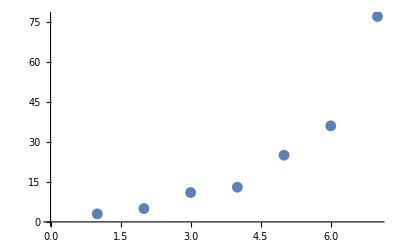
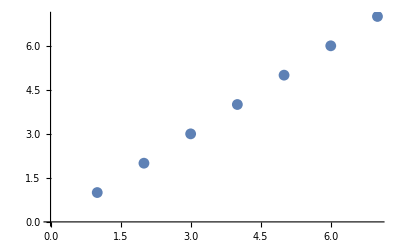
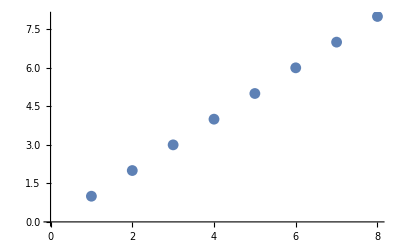

```mathematica
Map[ListPlot,{liste3,liste4,liste5}]
```

→ Tracer une liste en représentant la ligne qui joint les points ;

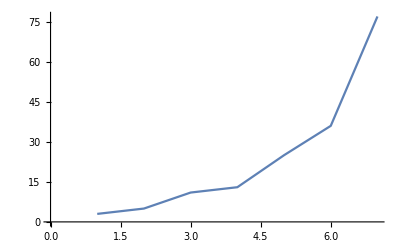

```mathematica
ListPlot[liste3,Joined->True]
```

On peut le faire aussi avec ListLinePlot[] :

```mathematica
ListLinePlot[liste3]==ListPlot[liste3,Joined->True]
ListLinePlot[liste3]
```

True

-Graphics-

#### 2. Tracer une liste de deux coordonnées

→ Tracer une liste des points ayant deux coordonnées, l’abscisse est la première des coordonnées et l’ordonnée la seconde :

```mathematica
liste7=Table[{i,i^2},{i,3.1,8.5,0.5}]
```

{{3.1,9.61},{3.6,12.96},{4.1,16.81},{4.6,21.16},{5.1,26.01},{5.6,31.36},{6.1,37.21},{6.6,43.56},{7.1,50.41},{7.6,57.76},{8.1,65.61}}

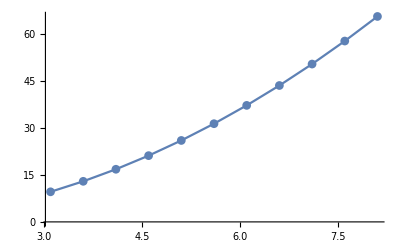

```mathematica
ListPlot[liste7,Joined->True,PlotMarkers->Automatic]
```

Notez que les points sont rendus visibles avec l’option : PlotMarkers→Automatic

#### 3. Tracer une liste à trois entrées

→ Examinez l’exemple :

```mathematica
liste8=Table[Cos[i]Cos[j],{i,0,2π,0.6},{j,0,2π,0.6}];
```

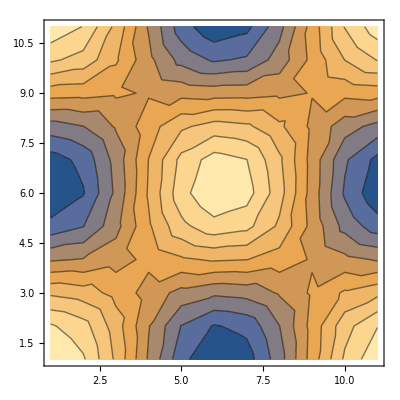

```mathematica
ListContourPlot[liste8]
```

#### 4. Tracer une liste à quatre entrées

→ Examinez l’exemple :

```mathematica
liste8=Table[
Cos[i+k(π/30)]Cos[j],
{i,0,2π,0.6},{j,0,2π,0.6},{k,0,30,1}
];
```

```mathematica
ListAnimate[
Map[
ListContourPlot,
liste8
]
]
```

#### 5. Mise en forme de listes avec TableForm[]

→ Affichez liste7 sous forme de tableau qu’on appellera liste7MiseEnForme :
	 on utilisera la fonction TableForm[]

```mathematica
?TableForm
```

Rappelons liste7 :

```mathematica
liste7
```

{{3.1,9.61},{3.6,12.96},{4.1,16.81},{4.6,21.16},{5.1,26.01},{5.6,31.36},{6.1,37.21},{6.6,43.56},{7.1,50.41},{7.6,57.76},{8.1,65.61}}

```mathematica
liste7MiseEnForme=TableForm[liste7]
```

3.1 | 9.61
3.6 | 12.96
4.1 | 16.81
4.6 | 21.16
5.1 | 26.01
5.6 | 31.36
6.1 | 37.21
6.6 | 43.56
7.1 | 50.41
7.6 | 57.76
8.1 | 65.61

→ Testez liste7*3 et liste7MiseEnForme*3 :

```mathematica
liste7*3
liste7MiseEnForme*3
```

{{9.3,28.83},{10.8,38.88},{12.3,50.43},{13.8,63.48},{15.3,78.03},{16.8,94.08},{18.3,111.63},{19.8,130.68},{21.3,151.23},{22.8,173.28},{24.3,196.83}}

3 3.1 | 9.61
3.6 | 12.96
4.1 | 16.81
4.6 | 21.16
5.1 | 26.01
5.6 | 31.36
6.1 | 37.21
6.6 | 43.56
7.1 | 50.41
7.6 | 57.76
8.1 | 65.61

## III. Programmation fonctionnelle et Programmation par règles

En première approximation, ce sont deux modes de programmation très proches dans l’esprit, qui diffèrent principalement par leur mode d’écriture.

#### 1. ReplaceAll[] et Rule[]

→ Expliquez quelle est la différence entre :

```mathematica
(x+3y)/.{x->y,y->z}
```

y+3 z

```mathematica
(x+3y)/.{x->y}/.{y->z}
```

4 z

Un brin d’ADN list9 est constitué de nucléotides : A, T, G, C.

```mathematica
list9={A,C,G,T,G,T,A,C,G,T,G,T}
```

{A,C,G,T,G,T,A,C,G,T,G,T}

→ Remplacez dans liste9 tous les A par T, les T par A, les G par C, et les C par G (pour avoir la séquence du brin complémentaire)

```mathematica
list9/.{A->T,T->A,G->C,C->G}
```

{T,G,C,A,C,A,T,G,C,A,C,A}

## IV. Traitement d’expressions symboliques

### A. Transformations algébriques

#### 1. Expand[] et Factor[]

→ Développer et factoriser : -1/2 ((1-√a)^8-(1+√a)^8) ((1-√a)^8+(1+√a)^8) √a

```mathematica
Expand[-1/2 ((1-√a)^8-(1+√a)^8) ((1-√a)^8+(1+√a)^8) √a]
```

16 a+560 a^2+4368 a^3+11440 a^4+11440 a^5+4368 a^6+560 a^7+16 a^8

```mathematica
Factor[-1/2 ((1-√a)^8-(1+√a)^8) ((1-√a)^8+(1+√a)^8) √a]
```

16 a (1+a) (1+6 a+a^2) (1+28 a+70 a^2+28 a^3+a^4)

### B. Réarrangements algébriques

→ Factoriser x^2-3 avec Mathematica.

```mathematica
Factor[x^2-3]
```

-3+x^2

→ Soit f[x]=((x+3)(x-1)^2)/((x^2+1)(x+5)^2). Utiliser les fonctions Expand, ExpandAll, ExpandDenominator et ExpandNumerator pour f[x] et commenter les résultats.

```mathematica
f[x]=((x+3)(x-1)^2)/((x^2+1)(x+5)^2);
```

```mathematica
Expand[f[x]]
ExpandAll[f[x]]
ExpandDenominator[f[x]]
ExpandNumerator[f[x]]
```

3/((5+x)^2 (1+x^2))-(5 x)/((5+x)^2 (1+x^2))+x^2/((5+x)^2 (1+x^2))+x^3/((5+x)^2 (1+x^2))

3/(25+10 x+26 x^2+10 x^3+x^4)-(5 x)/(25+10 x+26 x^2+10 x^3+x^4)+x^2/(25+10 x+26 x^2+10 x^3+x^4)+x^3/(25+10 x+26 x^2+10 x^3+x^4)

((-1+x)^2 (3+x))/(25+10 x+26 x^2+10 x^3+x^4)

(3-5 x+x^2+x^3)/((5+x)^2 (1+x^2))

→ Rechercher les fonctions Mathematica qui transforment (en une ou plusieurs étapes) f(x)=1/(x^2-16)-(x+4)/(x^2-3 x-4) en g[x]=(-15-7 x-x^2)/(-16-16 x+x^2+x^3)

```mathematica
f[x]=1/(x^2-16)-(x+4)/(x^2-3 x-4);
g[x]=(-15-7 x-x^2)/(-16-16 x+x^2+x^3);
```

```mathematica
Expand[f[x]]
ExpandAll[f[x]]
ExpandDenominator[f[x]]
ExpandNumerator[f[x]]
```

3/((5+x)^2 (1+x^2))-(5 x)/((5+x)^2 (1+x^2))+x^2/((5+x)^2 (1+x^2))+x^3/((5+x)^2 (1+x^2))

3/(25+10 x+26 x^2+10 x^3+x^4)-(5 x)/(25+10 x+26 x^2+10 x^3+x^4)+x^2/(25+10 x+26 x^2+10 x^3+x^4)+x^3/(25+10 x+26 x^2+10 x^3+x^4)

((-1+x)^2 (3+x))/(25+10 x+26 x^2+10 x^3+x^4)

(3-5 x+x^2+x^3)/((5+x)^2 (1+x^2))

### C. Transformer des expressions trigonométriques

→ Comparer et commenter les trois résultats des fonctions TrigExpand, TrigReduce et TrigFactor appliquées à f(x)=(sin(x))^2+(tan(x))^2

```mathematica
f[x]=(sin(x))^2+(tan(x))^2;
TrigExpand[f[x]]
TrigReduce[f[x]]
TrigFactor [f[x]]
```

1/2+tan^2 x^2-Cos[x]^2/2+Sin[x]^2/2

1/2 (1+2 tan^2 x^2-Cos[2 x])

1/2 (1+2 tan^2 x^2-Cos[2 x])

→ Vérifier les identités trigonométriques suivantes :
	sin(a + b) = sin(a) cos(b) + cos(a) sin(b)
	(1 − (cot(a))^2 + (1 − (tan(a)))^2 =(sec(a)−csc(a))^2

```mathematica
TrigExpand[Sin[a + b]] == TrigExpand[Sin[a] Cos[b] + Cos[a] Sin[b]]
TrigExpand[1−(Cot[a])^2+(1−Tan[a])^2] ==TrigExpand[Sec[a]−(Csc[a])^2]
```

True

3/2+Cot[a]-Cot[a]^2/4-Csc[a]^2-Csc[a] Sec[a]+Sec[a]^2+1/4 Csc[a]^2 Sec[a]^2-Tan[a]-Tan[a]^2/4==-Csc[a]^2+Sec[a]